```mathematica
Ejercicio. 5.2.
Considera la curva en R dada por las ecuaciones paramétricas:
donde t es el parámetro.
(1) Determina la ecuación implícita que define esta curva. En esta expresión aparece un parámetro
a; según los diferentes valores de a, tendremos diferentes curvas.
(2) Dibuja esta curva mediante la orden de Mathematica “ParametricPlot”, para los valores de a =
(3) Dibuja la curva, dada por la ecuación implícita, mediante la orden de Mathematica “ContourPlot”,
para los valores de a
```

```mathematica
(1)Despejamos t e igualamos:
```

```mathematica
Solve[z-(n*y^2)/(y^2+n^2)==0,y]
```

{{y→-(n √z)/(√(n-z))},{y→(n √z)/(√(n-z))}}

```mathematica
Solve[z-(y^3)/(y^2+n^2)==0,y]
```

{{y→1/3 (z-(2^(1/3) z^2)/((-27 n^2 z-2 z^3+3 √3 √(27 n^4 z^2+4 n^2 z^4))^(1/3))-((-27 n^2 z-2 z^3+3 √3 √(27 n^4 z^2+4 n^2 z^4))^(1/3))/2^(1/3))},{y→z/3+((1+ⅈ √3) z^2)/(3 2^(2/3) (-27 n^2 z-2 z^3+3 √3 √(27 n^4 z^2+4 n^2 z^4))^(1/3))+((1-ⅈ √3) (-27 n^2 z-2 z^3+3 √3 √(27 n^4 z^2+4 n^2 z^4))^(1/3))/(6 2^(1/3))},{y→z/3+((1-ⅈ √3) z^2)/(3 2^(2/3) (-27 n^2 z-2 z^3+3 √3 √(27 n^4 z^2+4 n^2 z^4))^(1/3))+((1+ⅈ √3) (-27 n^2 z-2 z^3+3 √3 √(27 n^4 z^2+4 n^2 z^4))^(1/3))/(6 2^(1/3))}}

```mathematica
tomaremos solo las reales obteniendo dos parametrizaciones (de dos colas) según el signo ( lo pongo con los parametros del enunciado) :(a √x)/(√(a-x))-1/3 (y-(2^(1/3) y^2)/((-27 a^2 y-2 y^3+3 √3 √(27 a^4 z^2+4 a^2 y^4))^(1/3))-((-27 a^2 y-2 y^3+3 √3 √(27 a^4 y^2+4 a^2 y^4))^(1/3))/2^(1/3))=0
```

```mathematica
(2) dibujamos:
```

```mathematica
ParametricPlot[{0.5*t^2/(t^2+0.5^2),t^3/(t^2+0.5^2)},{t,-1,1}]
```

-Graphics-

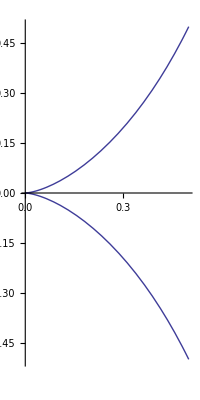

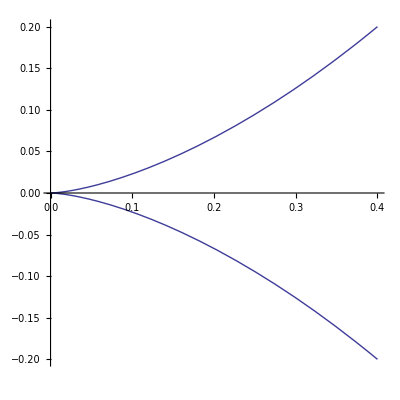

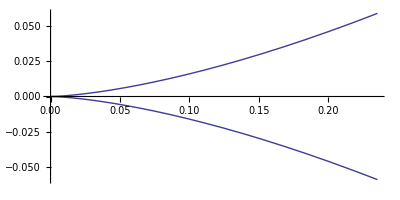

```mathematica
ParametricPlot[{t^2/(t^2+1^2),t^3/(t^2+1^2)},{t,-1,1}]
ParametricPlot[{2*t^2/(t^2+2^2),t^3/(t^2+2^2)},{t,-1,1}]
ParametricPlot[{4*t^2/(t^2+4^2),t^3/(t^2+4^2)},{t,-1,1}]
```

```mathematica
(3) Evaluamos con counterplot según a
```

```mathematica
ContourPlot[ (1 √r)/(√(1-r))-1/3 (p-(2^(1/3) p^2)/((-27*1^2 p-2 p^3+3 √3 √(27*1^4 p^2+4*1^2 p^4))^(1/3))-((-27*1^2 p-2 p^3+3 √3 √(27*1^4 p^2+4*1^2 p^4))^(1/3))/2^(1/3))==0 ,{r,-1,1},{p,-1,1}]
```

-Graphics-